# Initial conditions

```mathematica
(*we keep the same values for unrescaled quantities as the numerical solution notebook for matching*)
```

```mathematica
(*Keep m1 > m2. Set Rinit and Pinit so that you start at the point of closest distance. Keep PN parameter small: ϵ ->0, P ->0, 1/R -> 0,  spins/(orb. ang. momentum) -> 0*)

m1=5/2;m2=1;G=1 ;
ϵ= 5/1000; 
tfin = 500/ϵ;
precisionGoal=Automatic (*50*) ;

spinSuppressFac = ϵ^(1/2);    c = 1/spinSuppressFac   ;    kGoldstein = G M μ ;
Rinit=1{ 3,0,0};
Pinit=1{0,-1,0};
S1init={0,1,1}/kGoldstein spinSuppressFac;         
S2init={1,-3/10,0}/kGoldstein spinSuppressFac;
(*These spin numbers (times spinSuppressFac) entered by user are unscaled quantities. But S1init and S2init are scaled (reduced) spins*)
S1ninit = Norm[S1init];
S2ninit = Norm[S2init];
rinit=Rinit/(G M)     ;     pinit=Pinit/μ ;
Linit=Cross[rinit,pinit] ;     Lninit = Norm[Linit] ;
M = m1+m2 ;  μ = m1 m2/M ;
δ1=2 m1 m2/M^2 (1+3/4 m2/m1)  ;δ2=2 m2 m1/M^2 (1+3/4 m1/m2) ; 

(*Prepare  a sign function for later use in solution*)

If [ δ2/(c^2 Norm[rinit]^3 S1ninit Lninit)Linit.Cross[S1init, S2init]   > 0, sign =1, sign =-1 ] ;
```

```mathematica
Jvec= Linit + S1init + S2init  ;  J = Norm[Jvec] ;

sphericalAngles[V_]:=Module[{Jx,Jy,Jz},
polarAngJ = ToSphericalCoordinates[V][[2]];
azimuthAngJ =  ToSphericalCoordinates[V][[3]];
Return[{polarAngJ,azimuthAngJ}] ; ];

vectorComponents[{V_, θ_, ϕ_}]:=Module[{Vx,Vy,Vz},
Vz = V Cos[θ];
Vx=V Sin[θ]Cos[ϕ];  
Vy=V Sin[θ]Sin[ϕ];
Return[{Vx, Vy, Vz}] ; ];

{ξ2, ξ1}=sphericalAngles[Jvec]+{0,π/2};

EulMat ={ {Cos[ξ1], Sin[ξ1],0},{-Sin[ξ1]Cos[ξ2], Cos[ξ1]Cos[ξ2], Sin[ξ2]},{Sin[ξ1]Sin[ξ2], -Cos[ξ1]Sin[ξ2], Cos[ξ2]}}      ;
  (* Frame A := the one in which the above components are given.

Euler matrix which when multiplies with a column containing components in Frame A yields components in the inertial frame whose z-axis is along J vector (total angular momentum).

Gives components: Basic frame --> J-vector centered frame
*)
```

# Un-rescaled/rescaled quantities

```mathematica
R = {Rx, Ry,Rz} ; P ={Px,Py,Pz};
S1= {S1x, S1y,S1z} ;    S2= {S2x, S2y,S2z} ;
S1n = Norm[S1] ;     S2n = Norm[S2] ;

Seff= (δ1 S1+ δ2 S2);
r=R/(G M);       p=P/μ;
L=Cross[r,p] ;(*Conserved quantities defined in terms of scaled variables*) 
Ln=Norm[L] ;
Jn=Norm[L+S1+S2];
SeffL= Seff.L ;
```

```mathematica
(*Evaluating σ1 and σ2*)
{Rx,Ry,Rz} = Rinit  ;
{Px,Py,Pz}=Pinit  ;
{S1x,S1y,S1z} = S1init ; 
{S2x,S2y,S2z} = S2init  ;

σ1=(S1.S2)/(S1n S2n) -Ln/S2n(δ1-δ2)/δ2(S1.L)/(Ln S1n) ;   (*σ1=Cos γ -L/S2(Q1-Q2)/Q2 Cos κ1 *)
σ2= (S2.L)/(Ln S2n) + (δ1 S1n)/(δ2 S2n)(S1.L)/(Ln S1n) ;           (*σ2= Cos κ2 +(Q1 S1)/(Q2 S2) Cos κ1*)
Enwt=(P.P)/(2 μ) -(G μ M)/Norm[R];(*Newtonian expression for energy*)
Lun=Norm[Cross[R,P]];  (*norm of unscaled ang momentum*)
e = (1 + 2 Enwt  Lun^2/(μ kGoldstein^2))^(1/2) ;(*Newtonian eccentricity in unrescaled variables*)
aUnrescaled= -kGoldstein/(2 Enwt) ;
a = aUnrescaled/(G M) ;
n = ((Ln/(a (1-e^2)^(1/2)))^3)/(G M) ;   (*unrescaled*)
```

# Cubic equation

```mathematica
A=2 Ln S1n δ1 (δ2-δ1);cubiceq=A x^3 -(Ln^2 (δ1-δ2)^2+2 δ2 Ln σ2 S2n  (δ2-δ1)+S1n^2 δ1^2+2 δ1 δ2 σ1 S1n S2n +δ2^2  S2n^2  )x^2+ (2  δ2 S2n (Ln σ1(δ2-δ1) +σ2( δ1 S1n+ δ2 σ1 S2n) )) x+-S2n^2 δ2^2 (σ1^2+σ2^2-1);(*=A(x -x1)(x -x2)(x -x3)*)
```

```mathematica
(*evaluate the cubic and find the roots*)
rtsol=Solve[cubiceq==0,x] ;
x2=x/.rtsol[[1]] ; 
x3=x/.rtsol[[2]] ;
x1=x/.rtsol[[3]];
{x2, x3, x1} = Sort[{x2, x3, x1}] ;
Clear[Rx, Ry, Rz, Px, Py, Pz, S1x, S1y, S1z, S2x, S2y, S2z, m1, m2]
```

# Solution of Cos[κ_1]

```mathematica
βe = e/(1+(1-e^2)^(1/2)) ;
ν = u + 2 ArcTan[ (βe Sin[u])/(1-βe Cos[u])]      ;(*same as ν= 2 ArcTan[√((1+e)/(1-e)) Tan[u/2]] but without the ArcTan issues*)

β = ((x3-x2)/(x1-x2))^(1/2);
α =  sign 2/(√(A(x1-x2)))EllipticF[ArcSin[√(((S1init.Linit)/(Lninit S1ninit)-x2)/(x3-x2))],β^2]   ;
Υ = 1/2 √(A(x1-x2))(α+(ν + e Sin[ν])/(c^2 Ln^3)) ;
cosκ1=x2+(x3-x2)JacobiSN[Υ,β^2]^2;
```

```mathematica
(*Evaluate coskp1*)
{Rx,Ry,Rz} = Rinit  ;
{Px,Py,Pz}=Pinit  ;
{S1x,S1y,S1z} = S1init ; 
{S2x,S2y,S2z} = S2init  ; 

findu[t_?NumericQ]:=FindRoot[n t == u - e Sin[u],{u,n t, n t - 2 π, n t + 2 π}, PrecisionGoal->precisionGoal];
```

```mathematica
fcosκ1[t_?NumericQ]:=cosκ1/.findu[t];
(*p1 =          ;*)
(*p2=Plot[fcosκ1[t],{t,0,tfin},PlotStyle->Red];
Show[p2,p1, PlotRange->All, ImageSize->Large]*)
(*Clear[Rx, Ry, Rz, Px, Py, Pz, S1x, S1y, S1z, S2x, S2y, S2z, m1, m2]
*)
```

# L vector solution

```mathematica
LinitJframe = EulMat.Linit      ;
Lξ10 =   sphericalAngles[LinitJframe][[2]]+ π/2 ;

α1 = -δ2 (J + Lninit + S2ninit σ2 )/(S1ninit(δ1-δ2)) ;
α2 = -δ2 (-J + Lninit + S2ninit σ2 )/(S1ninit(δ1-δ2)) ;
β1 = δ2 1/(2 S1ninit (δ1-δ2))(-(Lninit^2 δ1+ J^2 δ2+ S1ninit(δ1-δ2)(S1ninit+S2ninit σ1)+ Lninit S2ninit δ1 σ2 + J(Lninit(δ1+δ2)+S2ninit σ2 δ2)))  ;
β2 = δ2 1/(2 S1ninit (δ1-δ2))(-(Lninit^2 δ1+ J^2 δ2+ S1ninit(δ1-δ2)(S1ninit+S2ninit σ1)+ Lninit S2ninit δ1 σ2 - J(Lninit(δ1+δ2)+S2ninit σ2 δ2)))  ;
```

```mathematica
solPiece1 =(2/(A(x1-x2))^(1/2)) ((β1  EllipticPi[(x2-x3)/(α1+x2),JacobiAmplitude[Υ,β^2],β^2])/(α1+x2)-(β2 EllipticPi[(x2-x3)/(α2+x2),JacobiAmplitude[Υ,β^2],β^2])/(α2+x2))  ; 
solPiece2 =Lξ10 -(solPiece1/.u->0 )    ;
Lξ1sol=solPiece1 + solPiece2  ;
cosκ2[t_]:= σ2 -  δ1 S1ninit/(δ2 S2ninit) fcosκ1[t];
LvecAzimuthAngle[t_]:=-π/2+Lξ1sol/.findu[t];
LvecPolarAngle[t_]:= ArcCos[(Lninit^2+ Lninit S1ninit  fcosκ1[t] + Lninit S2ninit  cosκ2[t]  )/(Lninit J)]; 
Lsol[t_]:=Module[{Lx,Ly,Lz},
{Lx,Ly,Lz} = vectorComponents[{Lninit, LvecPolarAngle[t],LvecAzimuthAngle[t]}];
Return[ kGoldstein(Inverse[EulMat].{Lx,Ly,Lz}) ]; ];
```

```mathematica
(*p1 =          ;
p2=Plot[Lsol[t][[2]],{t,0,tfin},PlotStyle->Red, ImageSize->Large];
Show[p1, p2]*)
```

```mathematica
(*Quit[];*)
```

# S1 vector solution

```mathematica
S1initJframe = EulMat.S1init      ;
S1ξ10 =   sphericalAngles[S1initJframe][[2]]+ π/2 ;

α1S1 =  (δ2 (-J+S1ninit+S2ninit σ1))/(Lninit δ1)  ;
α2S1 =(δ2 (J+S1ninit+S2ninit σ1))/(Lninit δ1) ;
β1S1 =-(δ2 (Lninit^2 δ1+(S1ninit (δ1-δ2)+J δ2) (-J+S1ninit+S2ninit σ1)+Lninit S2ninit δ1 σ2))/(2 Lninit δ1)  ;
β2S1 =(δ2 (-Lninit^2 δ1+(-S1ninit δ1+(J+S1ninit) δ2) (J+S1ninit+S2ninit σ1)-Lninit S2ninit δ1 σ2))/(2 Lninit δ1) ;

solPiece1S1 =(2/(A(x1-x2))^(1/2)) ((β1S1  EllipticPi[(x2-x3)/(α1S1+x2),JacobiAmplitude[Υ,β^2],β^2])/(α1S1+x2)-(β2S1 EllipticPi[(x2-x3)/(α2S1+x2),JacobiAmplitude[Υ,β^2],β^2])/(α2S1+x2))   + (ν + e Sin[ν])/Ln^3  (J δ2)/c^2  ;
solPiece1 =         (2/(A(x1-x2))^(1/2)) ((β1  EllipticPi[(x2-x3)/(α1+x2),JacobiAmplitude[Υ,β^2],β^2])/(α1+x2)-(β2 EllipticPi[(x2-x3)/(α2+x2),JacobiAmplitude[Υ,β^2],β^2])/(α2+x2))  ; 

solPiece2S1 =S1ξ10 -(solPiece1S1/.u->0 )    ;
S1ξ1sol=solPiece1S1 + solPiece2S1  ;

cosγ[t_]:= σ1 +   Lninit(δ1-δ2)/(δ2 S2ninit) fcosκ1[t];
S1vecAzimuthAngle[t_]:=-π/2+S1ξ1sol/.findu[t];
S1vecPolarAngle[t_]:= ArcCos[(S1ninit^2+ Lninit S1ninit  fcosκ1[t] + S1ninit S2ninit  cosγ[t]  )/(S1ninit J)]; 
S1sol[t_]:=Module[{S1x,S1y,S1z},
{S1x,S1y,S1z} = vectorComponents[{S1ninit, S1vecPolarAngle[t],S1vecAzimuthAngle[t]}];
Return[ kGoldstein(Inverse[EulMat].{S1x,S1y,S1z}) ]; ];
S2sol[t_]:=kGoldstein Jvec - Lsol[t]-S1sol[t];
```

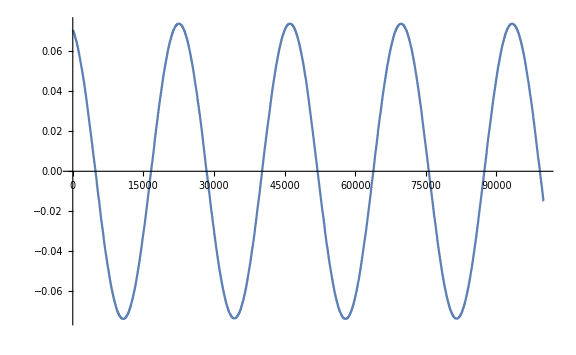
```mathematica
p1 =   -Graphics-       ;
p2=Plot[S2sol[t][[1]],{t,0,tfin},PlotStyle->Red, ImageSize->Large];
Show[p1,p2]
```

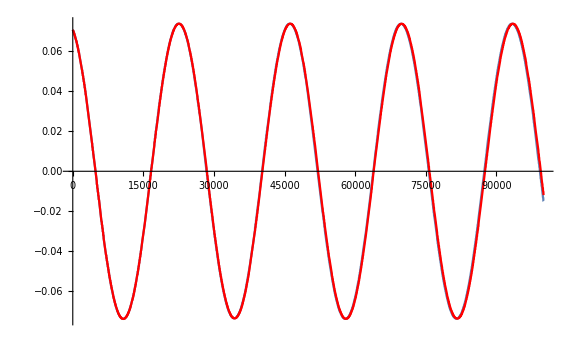

```mathematica
Quit[];
```